```mathematica
<< Задача 1.1.3>>
-Graphics-
-Graphics-
Условие:
-Graphics-
-Graphics-
Решение:
```

```mathematica
X=Cos[√B ψ] 1/Sin[ ψ];
Y=Sin[√B ψ] 1/Sin[ ψ];
```

```mathematica
<<Построим графики траектории движения точки (X[ψ],Y[ψ]) при нескольких значениях √B=b≠5 >>
<< b = 4 : >>
```

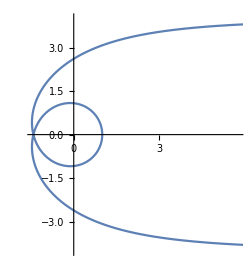

```mathematica
ParametricPlot[{Cos[√B ψ] 1/Sin[ ψ],Sin[√B ψ] 1/Sin[ ψ]}/.B->16,{ψ,0.0001,π-0.00001},PlotPoints->300]
```

```mathematica
<< b = 3 : >>
```

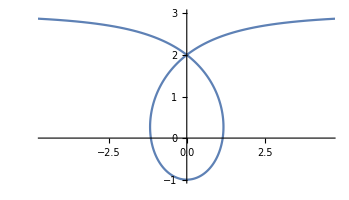

```mathematica
ParametricPlot[{Cos[√B ψ] 1/Sin[ ψ],Sin[√B ψ] 1/Sin[ ψ]}/.B->9,{ψ,0.0001,π-0.00001},PlotPoints->300]
```

```mathematica
<< b = 6 : >>
```

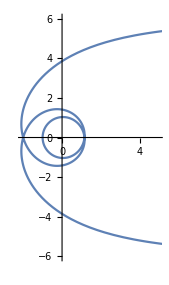

```mathematica
ParametricPlot[{Cos[√B ψ] 1/Sin[ ψ],Sin[√B ψ] 1/Sin[ ψ]}/.B->36,{ψ,0.0001,π-0.0001},PlotPoints->300]
```

```mathematica
<< Кривизна траектории  высчитывается при помощи следующего соотношения: K=[v×a]/(|v|^3) ([v×a]=Subscript[iv, x] Subscript[a, y]-Subscript[jv, y] Subscript[a, x], i,j=1) >>
```

```mathematica
FullSimplify[(1/((√(Csc[ψ]^2 (-1+B+Csc[ψ]^2)))^3))(-Csc[ψ] (Cos[√B ψ] Cot[ψ]+√B Sin[√B ψ]))(Csc[ψ] (-2 √B Cos[√B ψ] Cot[ψ]+(-B+Cot[ψ]^2+Csc[ψ]^2) Sin[√B ψ]))-(Csc[ψ] (√B Cos[√B ψ]-Cot[ψ] Sin[√B ψ]))(Csc[ψ] (Cos[√B ψ] (-B+Cot[ψ]^2+Csc[ψ]^2)+2 √B Cot[ψ] Sin[√B ψ]))]
```

Csc[ψ]^2 (-(√B Cos[√B ψ]-Cot[ψ] Sin[√B ψ]) (Cos[√B ψ] (-B+Cot[ψ]^2+Csc[ψ]^2)+2 √B Cot[ψ] Sin[√B ψ])-((Cos[√B ψ] Cot[ψ]+√B Sin[√B ψ]) (-2 √B Cos[√B ψ] Cot[ψ]+(-B+Cot[ψ]^2+Csc[ψ]^2) Sin[√B ψ]))/((Csc[ψ]^2 (-1+B+Csc[ψ]^2))^(3/2)))

```mathematica
<<Поскольку координаты зависят от времени, то имеет место запись:(Причем положим, что φ[t_]=π/2+ω*t и ω=π/3)>>
```

```mathematica
X[t_]=Cos[√B ψ[t]] 1/Sin[ ψ[t]];
Y[t_]=Sin[√B ψ[t]] 1/Sin[ ψ[t]];
ψ[t_]:=π/2+ω*t;
ω:=π/3
FullSimplify[D[{Cos[√B ψ[t]] 1/Sin[ ψ[t]],Sin[√B ψ[t]] 1/Sin[ ψ[t]]}, t]]
```

```mathematica
< Теперь выразим скорость как Subscript[X, t]'=Subscript[v, x][t] и Subscript[Y, t]'=Subscript[v, y][t]>>
```

{1/3 π Sec[(π t)/3] (-√B Sin[1/6 √B π (3+2 t)]+Cos[1/6 √B π (3+2 t)] Tan[(π t)/3]),1/3 π Sec[(π t)/3] (√B Cos[1/6 √B π (3+2 t)]+Sin[1/6 √B π (3+2 t)] Tan[(π t)/3])}

```mathematica
<< Теперь рассмотрим график скорости от времени>>
```

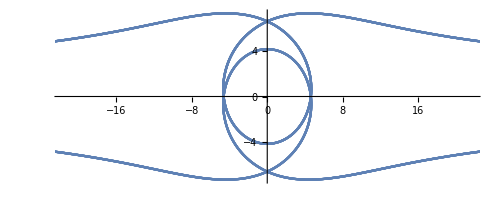

```mathematica
ParametricPlot[{1/3 π Sec[(π t)/3] (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]),-1/3 π Sec[(π t)/3] (√B Cos[1/6 √B π (-3+2 t)]+Sin[1/6 √B π (-3+2 t)] Tan[(π t)/3])}/. B->16,{t,-20,20}]
```

```mathematica
<<Поскольку абсолютная скорость v=√(Subscript[v, x]^2+Subscript[v, y]^2)>>
```

```mathematica
FullSimplify[√((1/3 π Sec[(π t)/3] (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]))^2+(-1/3 π Sec[(π t)/3] (√B Cos[1/6 √B π (-3+2 t)]+Sin[1/6 √B π (-3+2 t)] Tan[(π t)/3]))^2)]
```

1/3 π √(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))

```mathematica
<<Теперь получим график абсолютной скорости>>
```

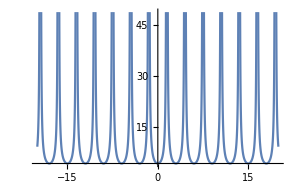

```mathematica
Plot[1/3 π √(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))/. B->16,{t,-20,20}]
```

```mathematica
<<Распишем ускорение как Subscript[X, t]''=Subscript[a, x][t] и Subscript[Y, t]''=Subscript[a, y][t]>>
```

```mathematica
FullSimplify[D[{Cos[√B ψ[t]] 1/Sin[ ψ[t]],Sin[√B ψ[t]] 1/Sin[ ψ[t]]}, t,t]]
```

{1/9 π^2 Sec[(π t)/3] (-Cos[1/6 √B π (3+2 t)] (1+B-2 Sec[(π t)/3]^2)-2 √B Sin[1/6 √B π (3+2 t)] Tan[(π t)/3]),1/9 π^2 Sec[(π t)/3] (-(1+B-2 Sec[(π t)/3]^2) Sin[1/6 √B π (3+2 t)]+2 √B Cos[1/6 √B π (3+2 t)] Tan[(π t)/3])}

```mathematica
<<Получим график ускорения>>
```

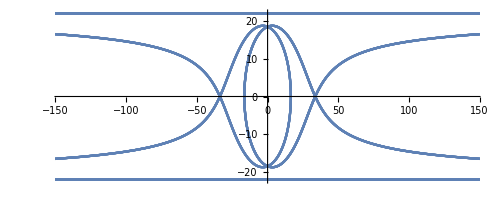

```mathematica
ParametricPlot[{1/9 π^2 Sec[(π t)/3] (-Cos[1/6 √B π (3-2 t)] (1+B-2 Sec[(π t)/3]^2)+2 √B Sin[1/6 √B π (3-2 t)] Tan[(π t)/3]),-1/9 π^2 Sec[(π t)/3] ((1+B-2 Sec[(π t)/3]^2) Sin[1/6 √B π (3-2 t)]+2 √B Cos[1/6 √B π (-3+2 t)] Tan[(π t)/3])}/. B->16,{t,-20,20}]
```

```mathematica
<<Поскольку абсолютное ускорение a=√(Subscript[a, x]^2+Subscript[a, y]^2)>>
```

```mathematica
FullSimplify[√((1/9 π^2 Sec[(π t)/3] (-Cos[1/6 √B π (3-2 t)] (1+B-2 Sec[(π t)/3]^2)+2 √B Sin[1/6 √B π (3-2 t)] Tan[(π t)/3]))^2+(-1/9 π^2 Sec[(π t)/3] ((1+B-2 Sec[(π t)/3]^2) Sin[1/6 √B π (3-2 t)]+2 √B Cos[1/6 √B π (-3+2 t)] Tan[(π t)/3]))^2)]
```

1/9 π^2 √(Sec[(π t)/3]^2 ((-1+B)^2+4 Sec[(π t)/3]^2 Tan[(π t)/3]^2))

```mathematica
<<Теперь рассмотрим график абсолютного ускорения >>
```

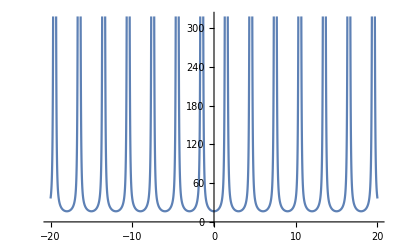

```mathematica
Plot[1/9 π^2 √(Sec[(π t)/3]^2 ((-1+B)^2+4 Sec[(π t)/3]^2 Tan[(π t)/3]^2))/. B->16,{t,-20,20}]
```

```mathematica
<<Единичный вектор вдоль траектории: (Subscript[v, x]/V;Subscript[v, y]/V) >>
```

```mathematica
FullSimplify[1/(1/3 π √(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))){1/3 π Sec[(π t)/3] (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]),-1/3 π Sec[(π t)/3] (√B Cos[1/6 √B π (-3+2 t)]+Sin[1/6 √B π (-3+2 t)] Tan[(π t)/3])}]
```

{(Sec[(π t)/3] (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]))/(√(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))),-(Sec[(π t)/3] (√B Cos[1/6 √B π (-3+2 t)]+Sin[1/6 √B π (-3+2 t)] Tan[(π t)/3]))/(√(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2)))}

```mathematica
<<Запросим график единичного вектора вдоль траектории>>
```

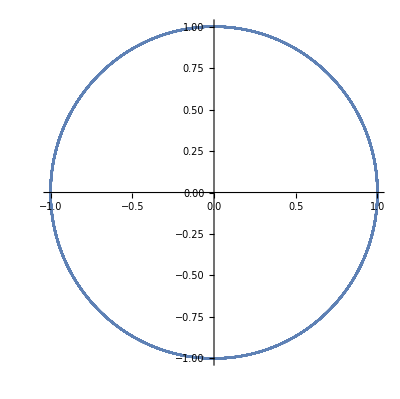

```mathematica
ParametricPlot[{(Sec[(π t)/3] (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]))/(√(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))),-((Sec[(π t)/3] (√B Cos[1/6 √B π (-3+2 t)]+Sin[1/6 √B π (-3+2 t)] Tan[(π t)/3]))/(√(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))))}/. B->16,{t,-20,20}]
```

```mathematica
<<Получим график зависимости скорости на ось х и у >>
```

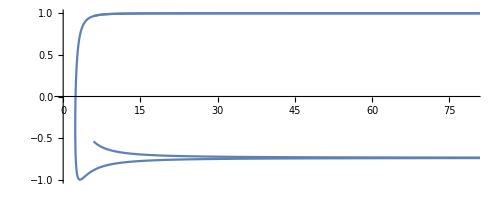

```mathematica
ParametricPlot[{1/3 π √(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2)),(1/(1/3 π √(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))))(1/3 π Sec[(π t)/3] (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]))}/.B->5,{t,-2,2}]
```

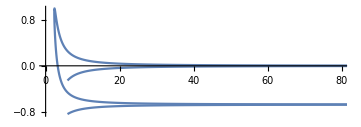

```mathematica
ParametricPlot[{1/3 π √(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2)),(1/(1/3 π √(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))))(-1/3 π Sec[(π t)/3] (√B Cos[1/6 √B π (-3+2 t)]+Sin[1/6 √B π (-3+2 t)] Tan[(π t)/3]))}/.B->5,{t,-2,2},PlotPoints->300]
```

```mathematica
<< Для нахождения единичного ускорения , воспользуемся тем, что оно равно еденичному вектору вдоль траектории (при ω=π/3))>>
```

```mathematica
FullSimplify[D[{(Sec[(π t)/3] (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]))/(√(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))),-((Sec[(π t)/3] (√B Cos[1/6 √B π (-3+2 t)]+Sin[1/6 √B π (-3+2 t)] Tan[(π t)/3]))/(√(Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))))}, t]]
```

{-((-1+B) √B π Sec[(π t)/3]^3 (√B Cos[1/6 √B π (3-2 t)]-Sin[1/6 √B π (3-2 t)] Tan[(π t)/3]))/(3 (Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))^(3/2)),-((-1+B) √B π Sec[(π t)/3]^3 (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]))/(3 (Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))^(3/2))}

```mathematica
<<Далее, найдем полное ускорение>>
```

```mathematica
FullSimplify[(-(((-1+B) √B π Sec[(π t)/3]^3 (√B Cos[1/6 √B π (3-2 t)]-Sin[1/6 √B π (3-2 t)] Tan[(π t)/3]))/(3 (Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))^(3/2))))^2+(-(((-1+B) √B π Sec[(π t)/3]^3 (√B Sin[1/6 √B π (3-2 t)]+Cos[1/6 √B π (3-2 t)] Tan[(π t)/3]))/(3 (Sec[(π t)/3]^2 (-1+B+Sec[(π t)/3]^2))^(3/2))))^2]
```

(4 (-1+B)^2 B π^2 Cos[(π t)/3]^4)/(9 (1+B+(-1+B) Cos[(2 π t)/3])^2)

```mathematica
<< Пусть (a[Subscript[t, 1]])'=0 => Subscript[t, 1] - время, в момент которого ускорение максимально при данном B >>
```

```mathematica
B:=16;
FullSimplify[D[{(4 (-1+B)^2 B π^2 Cos[(π t)/3]^4)/(9 (1+B+(-1+B) Cos[(2 π t)/3])^2)}, t]]
```

{-(12800 π^3 Cos[(π t)/3]^3 Sin[(π t)/3])/(3 (17+15 Cos[(2 π t)/3])^3)}

```mathematica
Solve[-(12800 π^3 Cos[(π t)/3]^3 Sin[(π t)/3])/(3 (17+15 Cos[(2 π t)/3])^3)==0,t]
```

{{t→ConditionalExpression[6 C[1],C[1]∈Integers]},{t→ConditionalExpression[(3 (-π/2+2 π C[1]))/π,C[1]∈Integers]},{t→ConditionalExpression[(3 (π/2+2 π C[1]))/π,C[1]∈Integers]},{t→ConditionalExpression[(3 (π+2 π C[1]))/π,C[1]∈Integers]}}

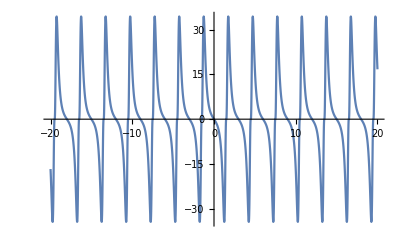

```mathematica
Plot[{-(12800 π^3 Cos[(π t)/3]^3 Sin[(π t)/3])/(3 (17+15 Cos[(2 π t)/3])^3)},{t,-20,20}]
```